```mathematica
data7={{6.25,0.0},{6.001765667929582,0.4991670832341408},{5.278004317051997,0.9933466539753061},{4.13971935999042,1.477601033306698},{2.6826721590673235,1.9470917115432527},{1.0290638906736893,2.397127693021015},{-0.6830632803695947,2.823212366975177},{-2.3117715943739867,3.2210884361884555},{-3.7234679805828397,3.586780454497614},{-4.804363328451665,3.916634548137417},{-5.4701460286861545,4.207354924039483},{-5.6730252461135064,4.456036800307177},{-5.4055342260972905,4.660195429836132},{-4.700772462711884,4.817790927085965},{-3.62908203253932,4.927248649942301},{-2.2914696179044554,4.987474933020272},{-0.810373552546205,4.997868015207525},{0.6813909728405793,4.958324052262343},{2.05251635929549,4.869238154390976},{3.1848542843027783,4.731500438437072},{3.983796907172315,4.546487134128409},{4.386467155241201,4.316046833244369},{4.366996872319622,4.0424820190979505},{3.938434841957967,3.7285260608836},{3.1511303019605785,3.377315902755753},{2.087754321004162,2.992360720519782},{0.8554229419387158,2.577506859107321},{-0.42435467375067093,2.136899401169149},{-1.6269859224456151,1.6749407507795233},{-2.63633383181035,1.19624664606991},{-3.3554384511104276,0.7056000402993361},{-3.715449005983995,0.20790331216645247},{-3.681958130522893,-0.2918707171379004},{-3.258165023178643,-0.7887284707162433},{-2.4845813971987143,-1.2777055101341583},{-1.435306822050832,-1.7539161384480992},{-0.21121038911135578,-2.2126022164742625},{1.0693642937964811,-2.649180704542467},{2.281529134967273,-3.0592894547135963},{3.3054259689726977,-3.4388307959198707},{4.037394751401694,-3.7840124765396412},{4.399719513203253,-4.091385555322054},{4.348062109859167,-4.357878862067941},{3.8759001316492907,-4.580829683747274},{3.0155535206251787,-4.758010369447581},{1.8356904891936137,-4.887650588325485},{0.43551986299002976,-4.968455018167322},{-1.0638243785898849,-4.999616287820504},{-2.529946600811446,-4.9808230441792025},{-3.8309547730765376,-4.912263063121662},{-4.847278975639672,-4.794621373315692},{-5.482485967105465,-4.629073411638661},{-5.672118447703113,-4.417273278600765},{-5.389760456496705,-4.161337211119504},{-4.649774834880334,-3.8638224377799357},{-3.5064531650285042,-3.5277016278519597},{-2.0496368572833727,-3.1563331893616042},{-0.39718177268071464,-2.753427712988188},{1.3150800368523572,-2.323010897068783},{2.9450042957329634,-1.8693833241511801},{4.3564009896360165,-1.3970774909946293},{5.4308248157476635,-0.9108125213604751},{6.07785134254383,-0.41544701408748197}};
```

```mathematica
data71=Join[data7,{data7[[1]]}];
```

```mathematica
bonusX=Transpose[data71][[1]]
```

{6.25,6.00177,5.278,4.13972,2.68267,1.02906,-0.683063,-2.31177,-3.72347,-4.80436,-5.47015,-5.67303,-5.40553,-4.70077,-3.62908,-2.29147,-0.810374,0.681391,2.05252,3.18485,3.9838,4.38647,4.367,3.93843,3.15113,2.08775,0.855423,-0.424355,-1.62699,-2.63633,-3.35544,-3.71545,-3.68196,-3.25817,-2.48458,-1.43531,-0.21121,1.06936,2.28153,3.30543,4.03739,4.39972,4.34806,3.8759,3.01555,1.83569,0.43552,-1.06382,-2.52995,-3.83095,-4.84728,-5.48249,-5.67212,-5.38976,-4.64977,-3.50645,-2.04964,-0.397182,1.31508,2.945,4.3564,5.43082,6.07785,6.25}

```mathematica
bonusY=Transpose[data71][[2]]
```

{0.,0.499167,0.993347,1.4776,1.94709,2.39713,2.82321,3.22109,3.58678,3.91663,4.20735,4.45604,4.6602,4.81779,4.92725,4.98747,4.99787,4.95832,4.86924,4.7315,4.54649,4.31605,4.04248,3.72853,3.37732,2.99236,2.57751,2.1369,1.67494,1.19625,0.7056,0.207903,-0.291871,-0.788728,-1.27771,-1.75392,-2.2126,-2.64918,-3.05929,-3.43883,-3.78401,-4.09139,-4.35788,-4.58083,-4.75801,-4.88765,-4.96846,-4.99962,-4.98082,-4.91226,-4.79462,-4.62907,-4.41727,-4.16134,-3.86382,-3.5277,-3.15633,-2.75343,-2.32301,-1.86938,-1.39708,-0.910813,-0.415447,0.}

```mathematica
{traX=Interpolation[bonusX,Method->"Spline"],traY=Interpolation[bonusY,Method->"Spline"]}
```

{InterpolatingFunction[…],InterpolatingFunction[…]}

```mathematica
fxy[t_]:={traX[t],traY[t]}
```

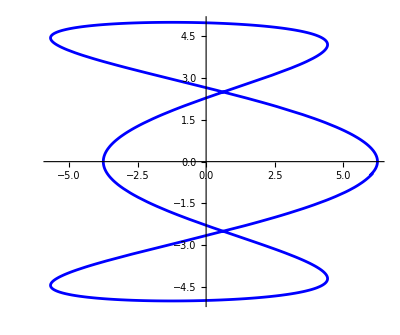

```mathematica
BonusPlot=ParametricPlot[fxy[t],{t,0,Length[data7]},PlotStyle->Blue]
```

```mathematica
PopupMenu[Dynamic[nreg],{6->"Hextagon",7->"Heptagon",8->"Octagon"}]
```

```mathematica
Object[color_,nreg_]:={color,RegularPolygon[{0,0},1,nreg]}
```

```mathematica
ObjectRotate[a_,s_,color_,nreg_]:=GeometricTransformation[Object[color,nreg],Composition[TranslationTransform[fxy[s]],RotationTransform[a]]]
```

```mathematica
BonusGrap[a_,s_,color_,nreg_]:=Graphics[ObjectRotate[a,s,color,nreg]]
```

```mathematica
ShowAllBonus[a_,s_,color_,nreg_]:=Show[BonusPlot,BonusGrap[a,s,color,nreg]]
```

```mathematica
ColorList=RandomColor[10]
```

{RGBColor[0.9334086620247593, 0.6875066963738239, 0.8799942593988912],RGBColor[0.7204222302542449, 0.45325753796413104, 0.2798392252570605],RGBColor[0.0980498093911717, 0.14244249196822523, 0.5230859667528995],RGBColor[0.1956533831143379, 0.5238674704838926, 0.5664914676095676],RGBColor[0.5904782681595602, 0.7004681896008198, 0.6397076001518982],RGBColor[0.5663361947395786, 0.672819123595948, 0.05323293228328252],RGBColor[0.5619705152341108, 0.476539360574076, 0.5001629557717304],RGBColor[0.641938066286996, 0.6901580076624123, 0.2590511486520233],RGBColor[0.9130199742217247, 0.2970285827231878, 0.8890508467146205],RGBColor[0.8887009757037483, 0.3110045070645806, 0.23702817963154144]}

```mathematica
Manipulate[ShowAllBonus[a,s,color,nreg],{a,0,2*Pi},{s,0,Length[data7]},{color,ColorList}]
```

```mathematica
Manipulate[ShowAllBonus[s,s,color,nreg],{s,0,Length[data7]},{color,ColorList}]
```